# Homework 2

1. x(t)=cos(2π f_1t)+cos(2π f_2t), f_1=0.5Hz, f_2=2Hz, f_s=10Hz, N=80, plot the
spectrum X(jf) of signal using DFT with N=80;
2. h_1(n)=[1 1 1 1], h_2 (n)=[1 1 1 1 1], plot the H_1(jf) and H_2(jf) using DFT
with N=100 respectively (f_s=10Hz);
3. Using conv function to compute the linear convolution y_1(n)=x(n)⋆h_1(n)
and y_2(n)=x(n)⋆h_2(n);

```mathematica
fs=10;(*采样频率*)
x=With[{f1=1/2,f2=2,n=80},(*从连续信号采样*)
Table[Cos[2π*f1*t]+Cos[2π*f2*t],{t,0,(n-1)/fs,1/fs}]//FullSimplify
];
```

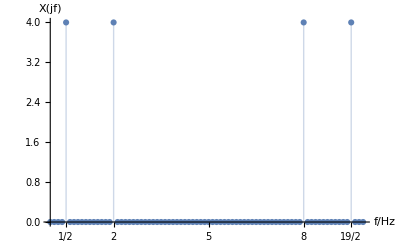

```mathematica
With[{n=80,t=1/fs},
ListPlot[{
{Table[fs*i/n,{i,0,n-1}],(*改变横轴坐标显示*)
t*Abs@Fourier[N[x,16],FourierParameters->{1,-1}]}ᵀ
},
Filling->Axis,AxesLabel->{"f/Hz","X(jf)"},
Ticks->{{1/2,2,5,8,19/2},Automatic}
]
]
```

```mathematica
h[1]=ConstantArray[1,4];
h[2]=ConstantArray[1,5];
```

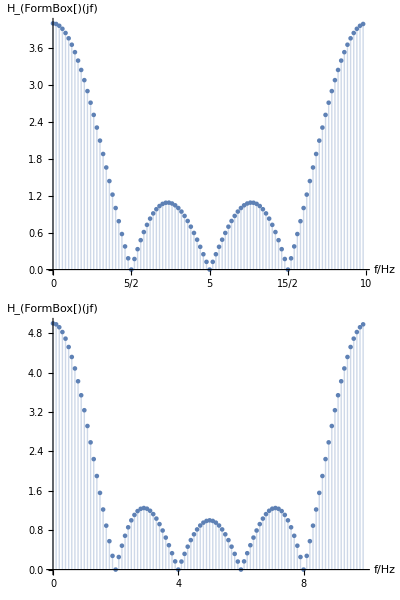

```mathematica
With[{n=100},
Column[Table[
ListPlot[{
{Table[fs*i/n,{i,0,n-1}],(*改变横轴坐标显示*)
Abs@Fourier[N[PadLeft[h[i],n],16],FourierParameters->{1,-1}]}ᵀ
},
Filling->Axis,AxesLabel->{"f/Hz",StringForm["H_(`1`)(jf)",i]},
Ticks->{Table[fs*j/Length[h[i]],{j,0,Length[h[i]]}],Automatic},
ImageSize->Medium
],
{i,{1,2}}],
Frame->All
]
]
```

```mathematica
linearConvolve[a_?ListQ,b_?ListQ]:=ListConvolve[a,b,{1,-1},0](*包装线性卷积函数*)
```

```mathematica
y[i_?IntegerQ]:=linearConvolve[x,h[i]]//FullSimplify
```

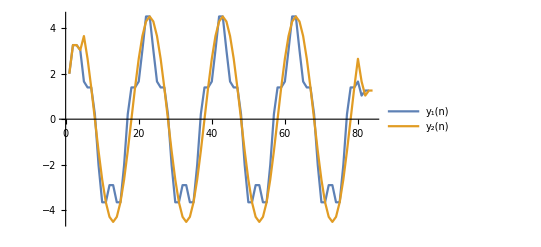

```mathematica
ListLinePlot[{y[1],y[2]},PlotLegends->{"y_1(n)","y_2(n)"}]
```

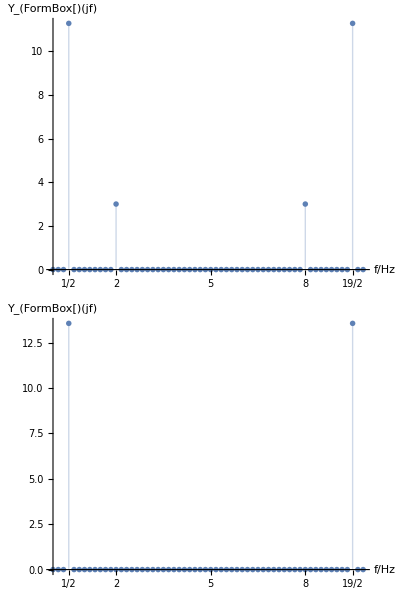

```mathematica
With[{t=1/fs,left=10,right=69},
Column[Table[
ListPlot[{
{Table[fs*i/(right-left+1),{i,0,right-left}],(*改变横轴坐标显示*)
t*Abs@Fourier[N[y[i][[left;;right]],100],FourierParameters->{1,-1}]}ᵀ
},
Filling->Axis,AxesLabel->{"f/Hz",StringForm["Y_(`1`)(jf)",i]},
Ticks->{{1/2,2,5,8,19/2},Automatic},
ImageSize->Medium
],
{i,{1,2}}],
Frame->All
]
]
```

## 结论：

将Y_1(jf) 和Y_2(jf) 与H_1(jf) 、H_2(jf) 以及X(jf) 比较，可以看出一个时域信号与系统的单位冲激响应卷积得到的信号对应的频域信号相当于原频域信号与系统传递函数的乘积。